# Re-running Axelrod's Tournament: Cooperation, Evolution, and Noise

## The iterated Prisoner's Dilemma in the Wolfram Language – from Tit-for-Tat to an evolutionarily stable mix that depends on noise

Wolfram Community submission – May 2026

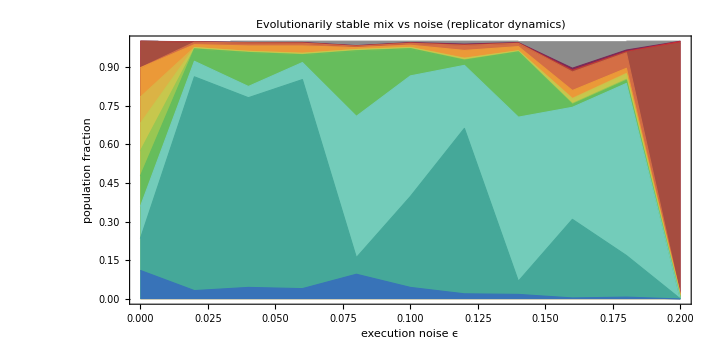

```mathematica
PostFigures`replicatorVsNoise[]
```

The headline result. As execution noise ϵ rises (left to right), the evolutionarily stable composition of strategies shifts – from a coexistence of generous reciprocators to a collapse into unconditional defection.

```mathematica
PostFigures`spatialMovieFrame[]   (* full movie: spatial_movie_compare.gif *)
```

Spatial IPD as a looping movie: low noise (left) sustains a rich mosaic of cooperative reciprocators; high noise (right) forces them into large defensive clusters of Grim and Tit-for-Tat, but cooperation never collapses. The static call above shows the final frame; the looping animation is spatial_movie_compare.gif (a single-world high-resolution version is spatial_movie.gif).

## Abstract

In 1980 Robert Axelrod ran a now-famous computer tournament for the iterated Prisoner's Dilemma. The winner was the simplest entrant of all – Tit-for-Tat: cooperate first, then copy your opponent. This notebook reproduces that tournament in the Wolfram Language, with the classic strategies plus modern entrants (Generous Tit-for-Tat, Pavlov, Gradual, and Press – Dyson zero-determinant strategies).

It then does two things Axelrod's setup hints at but does not show. First, an evolutionary tournament: we let populations of strategies reproduce in proportion to their success and ask which mixture is stable. Second, we add noise – a small probability that an intended move is mis-executed – and show that the evolutionarily stable mixture depends on the noise level. Finally, in the spirit of an automated-research loop, we let search algorithms discover new strategies – culminating in an eight-hour evolutionary search over memory-two strategies whose champion beats Tit-for-Tat by ~9% and finishes first in a field of 26, by learning to tell an accidental defection from a deliberate one.

## Setup (run this once if you want to evaluate the code)

You can skip this section if you only want to read. Every figure below is pre-rendered as a static image, so the prose, equations, and figures are all readable without evaluating anything.

If you do want to reproduce the figures, the project's two packages are attached alongside this notebook: axelrod.wl (the engine – payoffs, strategies, noisy match play, ranking) and post_figures.wl (one function per figure, each reading the committed data/ files and returning the graphic). The full analysis scripts that generated those data files live in wolfram/ and autoresearch/ in the repository. Run the cell below once; then every figure in the post is produced by the visible call shown just above it (e.g. PostFigures`replicatorVsNoise[]).

```mathematica
(* Put axelrod.wl, post_figures.wl and the data/ folder next to this notebook, then evaluate. *)
SetDirectory[NotebookDirectory[]];
Get["axelrod.wl"];          (* the IPD engine: Axelrod` context        *)
Get["post_figures.wl"];     (* figure functions: PostFigures` context  *)
```

## 1. The Prisoner's Dilemma, and why iteration changes everything

Two players each choose, simultaneously, to cooperate (C) or defect (D). The payoffs satisfy T > R > P > S and 2R > T + S. With the classic Axelrod values T=5, R=3, P=1, S=0:

| opp C | opp D
I C | R=3 | S=0
I D | T=5 | P=1

In a single game, defection strictly dominates: whatever the opponent does, you score more by defecting. Yet mutual cooperation (R=3 each) beats mutual defection (P=1 each). That is the dilemma. Axelrod's insight was that when the game is repeated, the shadow of the future can sustain cooperation – a strategy can reward cooperation and punish defection in later rounds.

### Encoding strategies in the Wolfram Language

We encode C = 1 and D = 0. A strategy is a pure function of the two histories of actual moves; the smallest interesting family is the memory-one strategies, parameterised by the probability of cooperating after each of the four possible previous outcomes:

```mathematica
memOne[open_, {pCC_, pCD_, pDC_, pDD_}] := Function[{me, opp},
  If[me === {},
    If[RandomReal[] < open, 1, 0],
    If[RandomReal[] < {pCC, pCD, pDC, pDD}[[ stateIndex[Last[me], Last[opp]] ]], 1, 0]]];

(* Tit-for-Tat: cooperate first, then copy the opponent's last move *)
TitForTat = memOne[1, {1, 0, 1, 0}];
Pavlov    = memOne[1, {1, 0, 0, 1}];   (* win-stay, lose-shift *)
GenerousTFT = memOne[1, {1, 1/3, 1, 1/3}];
```

The full library (in wolfram/axelrod.wl) has 13 strategies: AllC, AllD, Random, Tit-for-Tat, Suspicious TFT, Generous TFT, Tit-for-2-Tats, 2-Tits-for-Tat, Grim, Pavlov, Gradual, and two zero-determinant strategies (an extortioner and a generous one).

### Noise: the trembling hand

Real interactions are imperfect. We model execution noise: each intended move is flipped with probability ϵ, and the opponent sees the actual (post-noise) move. This single knob turns out to control everything that follows.

## 2. The classic round-robin (reproducing Axelrod 1980)

Every strategy plays every strategy (including itself) for 200 rounds, repeated 100 times to average out randomness. Each strategy's score is its mean per-round payoff against the whole field. At ϵ = 0 (no noise) the ranking is:

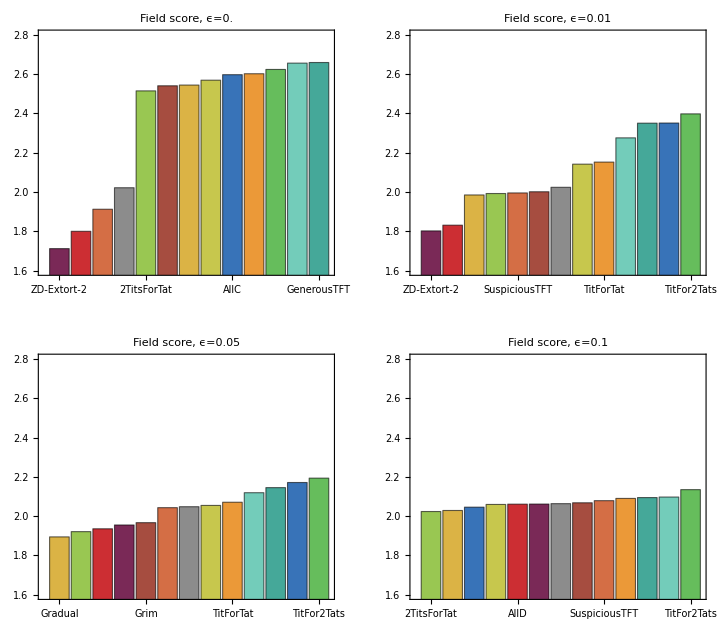

```mathematica
PostFigures`rankingGrid[]
```

Field score of each strategy at four noise levels. At ϵ=0 the generous reciprocators lead; the extortioner (ZD-Extort-2) finishes last.

The classic lesson holds. Nice, reciprocal, forgiving strategies dominate. Notably, plain Tit-for-Tat is edged out by its more forgiving cousins – Generous TFT and Tit-for-2-Tats – exactly the refinement Axelrod found in his second tournament. And the zero-determinant extortioner finishes dead last: extortion wins individual matches but poisons the cooperative environment it depends on.

The payoff structure of who-beats-whom:

```mathematica
PostFigures`payoffHeatmap[]
```

[ failed to evaluate: PostFigures`payoffHeatmap[] – is PostFigures` loaded? ]

Mean per-round payoff, row strategy against column strategy (ϵ=0). Warm = high. The cooperative cluster (top-left block) sustains mutual R=3; AllD and the extortioner do well in single matchups but drag the whole field down.

### What noise does to the ranking

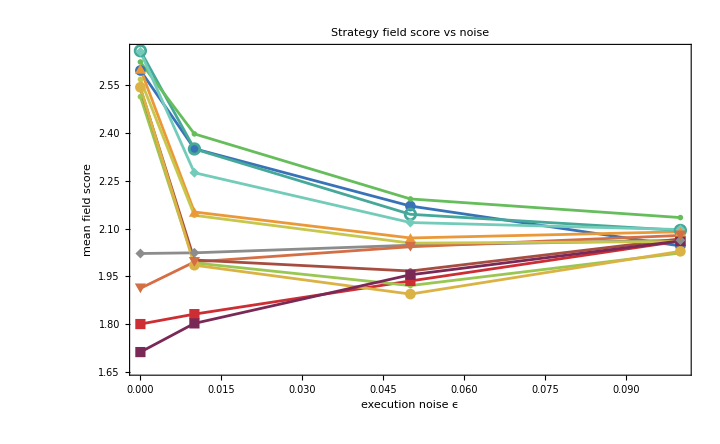

```mathematica
PostFigures`scoreVsNoise[]
```

As noise rises, every strategy's score is pulled toward the mutual-defection payoff P=1, and the gap between 'nice' and 'nasty' strategies narrows. Unforgiving strategies (Grim, Gradual) fall fastest: a single accidental defection traps them in retaliation.

## 3. The evolutionary tournament – the stable mix depends on noise

Axelrod's deeper question was evolutionary: if successful strategies reproduce, which ones survive? We answer it two ways.

### Replicator dynamics

Let x be the vector of population fractions and A the mean-payoff matrix (A[i,j] = score of i against j). Each strategy grows in proportion to its fitness relative to the population average:

x_i'=x_i((A.x)_i-x.A.x)

```mathematica
replicator[A_, steps_, mut_] := Module[{x = ConstantArray[1./n, n], f, phi},
  Do[ f = A . x; phi = x . f;
      x = x f / phi;              (* selection           *)
      x = (1 - mut) x + mut/n;    (* small mutation term  *)
      x = x / Total[x],
    {steps}];
  x]
```

Sweeping the noise level and recording the stable composition gives the headline figure (top of this post). It reveals three regimes:

Low noise (ϵ ≈ 0): a coexistence of cooperative strategies – Generous TFT, Tit-for-2-Tats, ZD-Generous, Tit-for-Tat and Pavlov share the population. Cooperation is evolutionarily robust.

Intermediate noise: the forgiving reciprocators (Generous TFT, Tit-for-2-Tats, ZD-Generous) dominate and trade the lead among themselves – error-correction is at a premium.

High noise (ϵ ≥ 0.2): cooperation collapses. A single unforgiving punisher – Grim – sweeps to ~98% of the population: under heavy noise, reciprocators spend so long accidentally punishing each other that a strategy which simply defects forever after the first defection becomes the only stable attractor (once noise has triggered it, it is behaviourally identical to AllD).

### A finite-population check: the Moran process

Replicator dynamics is a deterministic, infinite-population limit. To confirm the result is not an artefact of that idealisation, we also run a stochastic Moran process (population N=100, frequency-dependent birth-death with rare mutation) and record the long-run average composition.

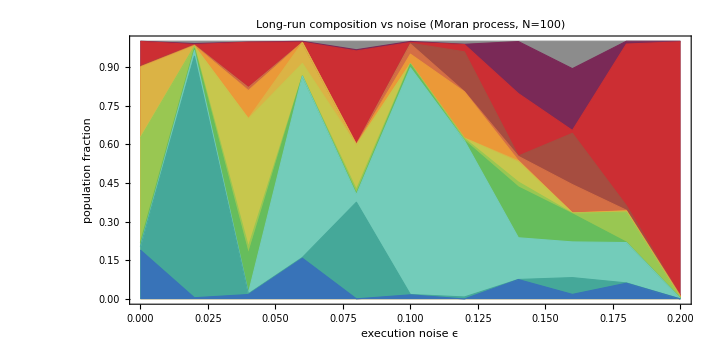

```mathematica
PostFigures`moranVsNoise[]
```

Moran process, long-run composition vs noise. Finite-population stochasticity makes the picture grainier, but the qualitative story survives: forgiving cooperators at low-to-moderate noise, defection-dominated outcomes as noise grows.

Takeaway. "Which strategy is evolutionarily stable?" has no noise-independent answer. The same population that converges on generous reciprocity in a clean channel converges on pure defection in a noisy one.

## 4. Discovering strategies that beat Tit-for-Tat under noise

Can we do better than the textbook strategies? In the spirit of an automated-research loop – propose → evaluate → accept → repeat – we search the memory-one space θ = (open, pCC, pCD, pDC, pDD) ∈ [0,1]^5 for the best response to the standard field at each noise level. A greedy hill-climb gives the narrative; a small genetic algorithm is the workhorse.

```mathematica
fitness[theta_, eps_] := Mean[
   meanMatch[memOne[theta[[1]], theta[[2;;]]], #, rounds, eps, reps][[1]] & /@ field];

(* greedy accept/reject loop -- the autoresearch analogy *)
champion = {1, 1, 0, 1, 0};                       (* start from Tit-for-Tat *)
Do[ proposal = clip[champion + RandomVariate[NormalDistribution[0, .12], 5]];
    If[fitness[proposal, eps] > fitness[champion, eps], champion = proposal],
  {150}]
```

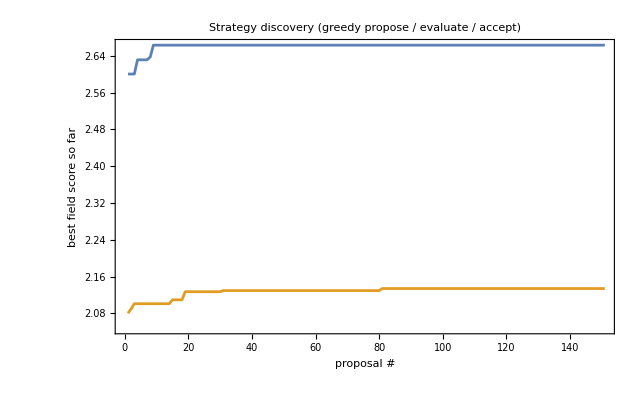

```mathematica
PostFigures`discoveryProgress[]
```

Greedy discovery: best field score found so far, starting from Tit-for-Tat, at two noise levels. Each upward step is an accepted proposal.

### The discovered strategies beat Tit-for-Tat at every noise level

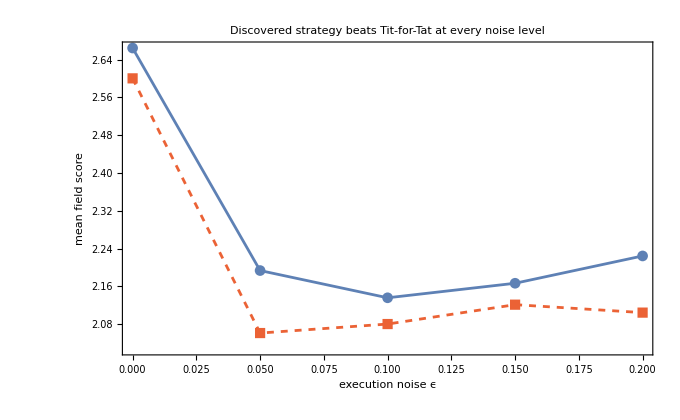

```mathematica
PostFigures`discoveredVsTFT[]
```

Discovered best-response strategy (solid) vs plain Tit-for-Tat (dashed) in field score, across noise. The discovered strategy wins everywhere; the margin is largest where noise matters most.

And the shape of the optimal strategy drifts with noise:

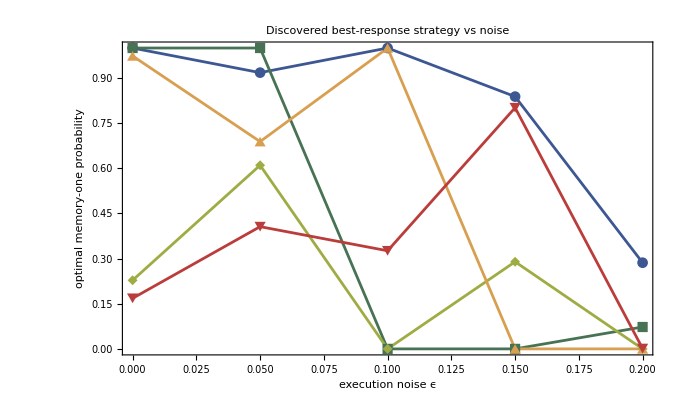

```mathematica
PostFigures`discoveredParams[]
```

The discovered memory-one probabilities vs noise. The forgiveness parameter pCD (cooperate again after being suckered) rises with noise – error-correction becomes essential – until, at very high noise, the best response against a decaying field tilts back toward defection.

This is the same lesson as the evolutionary tournament, reached by a different route: the optimal behaviour is a function of the environment, and noise is the knob that turns generous reciprocity into defection.

## 5. Letting an automated-research loop invent strategies

The discovery in §4 searched a continuous parameter box. We can also run the loop the way a human researcher would: propose a named hypothesis, evaluate it, keep it if it wins, repeat – exactly the shape of Karpathy-style autoresearch scaffolds (an AI edits one solution file; a fixed harness scores it; improvements are committed). We ported that loop to this domain: autoresearch/run_search.wls is the fixed harness (an 18-strategy field × six noise levels) and a sequence of hypotheses is proposed, each scored by mean field score averaged over the noise sweep.

champion <- Tit-for-Tat
LOOP:  propose a strategy  ->  evaluate vs the field under noise
       if score > champion: keep (save to champions/)  else: revert
       append (iter, score, status, description) to results.tsv

The result is a research log. Against this field (TFT baseline 2.316), the loop found seven strategies that beat Tit-for-Tat. The winners are instructive:

Tit-for-2-Tats (2.400). Patience beats vigilance: absorbing a single (possibly accidental) defection before retaliating is the single biggest win.

Generous Tit-for-2-Tats and Generous TFT. Tolerance plus probabilistic forgiveness compounds the gain.

AdaptiveGenerous – a self-tuning entrant. It estimates the channel noise online (from how often the opponent's moves flip) and scales its own forgiveness to match – beating TFT with no hand-set forgiveness constant.

What lost is as telling as what won. Plain contrition and Win-Stay-Lose-Shift (Pavlov) scored below TFT in this well-mixed field – forgiveness has to be patient (two-strikes), not merely reflexive. Hold that thought: Pavlov's fortunes change once we add spatial structure.

## 6. Beyond memory-one: evolving finite-state machines

Memory-one strategies condition only on the previous round. Do richer strategies help? We let a genetic algorithm evolve finite-state (Mealy) machines – each a little automaton with up to four internal states, an action and a state-transition for every observed opponent move. This space contains TFT, Grim, Pavlov and much else; we verified it encodes TFT and Grim exactly before evolving it.

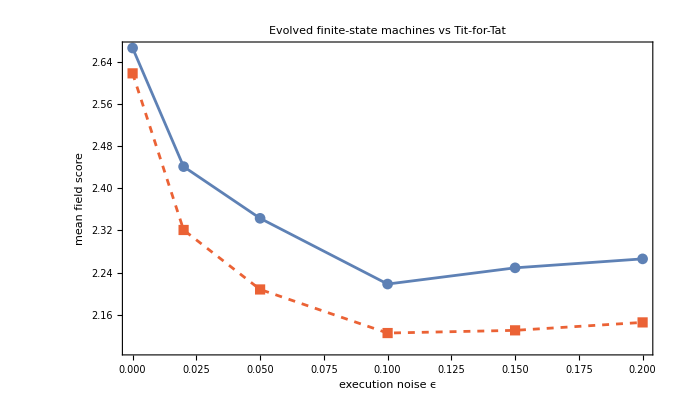

```mathematica
PostFigures`fsmVsTFT[]
```

Evolved finite-state machines vs Tit-for-Tat across noise – the machines beat TFT at essentially every noise level.

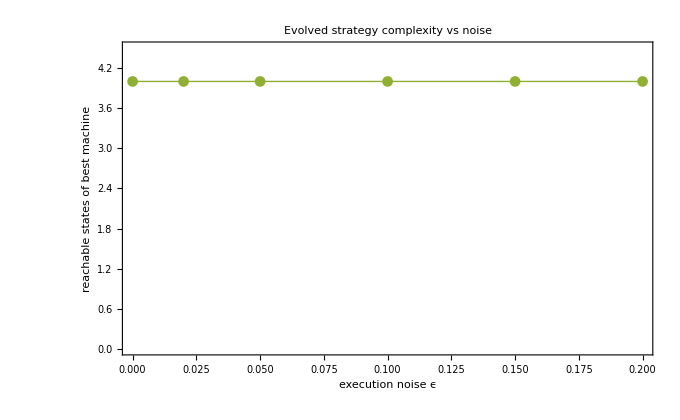

```mathematica
PostFigures`fsmComplexity[]
```

The best evolved machine uses 2–4 of its 4 reachable states – genuine multi-state memory, beyond what memory-one can express. The gain over the memory-one optimum is real but modest: against this field, most of the advantage is already captured by one round of memory plus the right amount of forgiveness.

## 7. Spatial structure makes cooperation robust to noise

Everything so far assumed a well-mixed population. But real agents interact locally. We place strategies on the sites of a 32×32 lattice (a torus). Each generation, every site plays its four neighbours and imitates fitter neighbours (Fermi rule). This is Nowak – May spatial game theory; the classic result is that clustering lets cooperators survive. We ask what noise does to it.

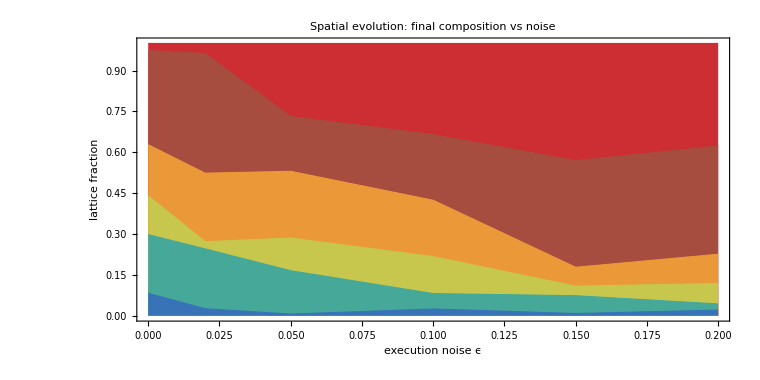

```mathematica
PostFigures`spatialComposition[]
```

Final lattice composition vs noise. At low noise the lattice is almost entirely cooperative reciprocators (Grim, Generous TFT, Tit-for-Tat), with unconditional defection nearly absent. As noise rises AllD gains ground – but never takes over: cooperation persists around 60% even at ϵ=0.2.

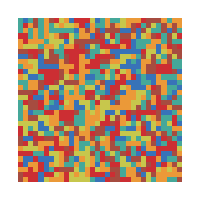
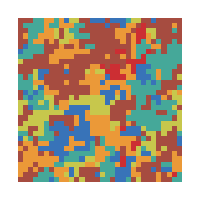
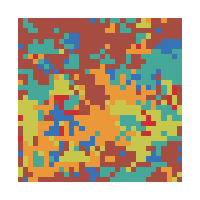
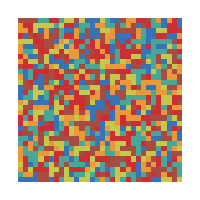
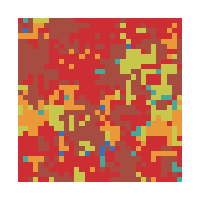
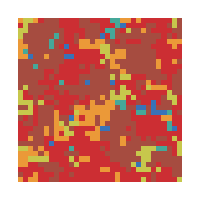
ϵ = 0 |  | 
-Graphics- | -Graphics- | -Graphics-
ϵ = 0.2 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
PostFigures`spatialSnapshots[]
```

Lattice snapshots (colours = strategies; legend below). Reciprocators survive by forming contiguous clusters that protect their cooperative interior. Noise frays the cluster boundaries but does not dissolve them.

```mathematica
PostFigures`spatialLegend[]
```

Spatial structure makes cooperation far more robust to noise. In the well-mixed model (§3), once ϵ is large the population collapses almost entirely to defection. On the lattice the same noise erodes cooperation only partially: clustering lets reciprocators shield one another, so cooperation degrades gracefully (97% → ~60%) instead of collapsing. Whether noise is catastrophic or merely corrosive for cooperation depends on population structure.

## 8. Red-Queen co-evolution

So far strategies were optimised against a fixed field. What if the field itself evolves? We co-evolve a population of memory-one genomes against itself: each individual's fitness is its score against the current population, which changes every generation. This is a Red Queen race – you must keep adapting just to hold your rank.

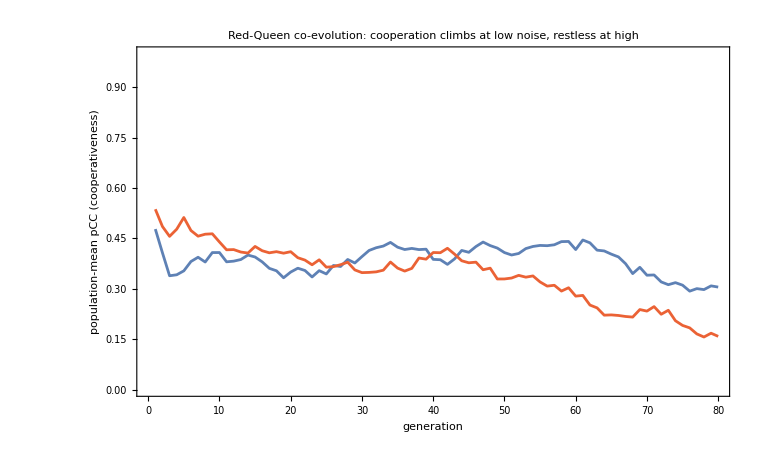

```mathematica
PostFigures`coevolutionTraj[]
```

Population-mean cooperativeness over generations. At ϵ=0 the population climbs to stable, highly cooperative reciprocity. At ϵ=0.15 it rises, then becomes restless and slides back – noise prevents a stable cooperative equilibrium from locking in.

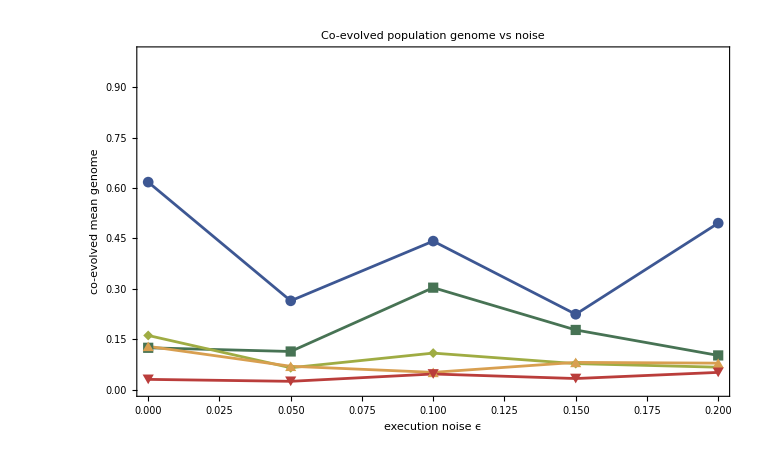

```mathematica
PostFigures`coevolutionGenome[]
```

The co-evolved mean genome vs noise. As noise rises the population becomes less rigidly cooperative (pCC falls) but more forgiving (pCD rises) and more able to recover from mutual defection (pDD rises) – a third independent route to the same conclusion: forgiveness answers noise.

## 9. Which strategies are evolutionarily stable?

A rigorous capstone. For a panel of 26 strategies (classics, modern entrants, and the discovered champions) we compute, at each noise level, the pairwise invasion matrix: can a rare mutant M invade a resident population of R? It can if A[M,R] > A[R,R]. A strategy is evolutionarily stable if no mutant can invade it.

```mathematica
PostFigures`essStabilityMap[]
```

[ failed to evaluate: PostFigures`essStabilityMap[] – is PostFigures` loaded? ]

Evolutionarily stable strategies vs noise (green = no mutant invades). At zero noise a whole cluster is uninvadable – AllD and Grim, but also Tit-for-Tat, ZD-Generous, Omega-TFT and even two of the discovered Generous-TFT champions: in a clean channel, cooperation can be evolutionarily stable. Add even a little noise and that cluster shatters – the stable set collapses to a lone defector (AllD or Grim), with noise levels in between admitting no pure ESS at all. Noise destroys the evolutionary stability of cooperation.

```mathematica
PostFigures`essInvasibilityHigh[]
```

[ failed to evaluate: PostFigures`essInvasibilityHigh[] – is PostFigures` loaded? ]

Invasibility matrix at ϵ=0.2 (red = row invades column). The defectors have the cleanest columns.

Three meanings of “stable.” “Which strategy is stable?” has three answers: (i) ESS (uninvadable) admits cooperation at zero noise but collapses to a lone defector once noise appears; (ii) replicator-stable from a cooperative start (§3) gives generous reciprocity collapsing to Grim under noise; (iii) spatially resilient (§7) gives reciprocator clusters that survive noise. All three are noise-dependent and they disagree – there is no single best strategy, only best-for-a-given-world.

## 10. An 8-hour automated search: a champion beyond memory-one

The discoveries so far searched small or fixed spaces. To see what a genuinely long, open-ended search would find, we ran the autoresearch loop for eight hours over a much larger space: memory-two stochastic strategies, θ = (open, p1, …, p16) ∈ [0,1]^17. A memory-two strategy conditions its move on the last two rounds, so it can express things memory-one cannot – crucially, it can tell an isolated defection (likely a noise blip) from a sustained one.

The engine was a 4-island genetic algorithm with ring migration and soft-restarts on stagnation, scored on the same field-vs-noise protocol, with a hall of fame and frequent checkpoints. It ran unattended under a supervisor that caps the wall-clock budget and guarantees no runaway kernels are left behind. Over 111 generations the best field score climbed steadily, then plateaued – the signature of a converged search:

Search progress: field score of the best strategy found, by generation (selected rows):

generation | best field score | vs TFT
5 | 2.4328 | +0.145
15 | 2.5144 | +0.226
25 | 2.5357 | +0.248
45 | 2.5507 | +0.263
75 | 2.5661 | +0.278
111 | 2.5661 | +0.278

### Honest scoring: searching is not the same as winning

The search ranks candidates with a fixed random seed so the comparison is deterministic. That can overfit the seed. So every hall-of-fame strategy was re-scored at high repetition with fresh seeds it never saw during the search, and to be doubly sure we then validated the winner on four more independent seeds. The champion's edge survives intact: a robust improvement of +0.20 over Tit-for-Tat (about 8.8%), essentially identical to its search-time score. It is a real strategy, not a seed artefact.

### What the champion does

Decoding the 17-number genome into behaviour reveals a clean, interpretable rule. It opens by cooperating (~90%), reciprocates cooperation, and – the key – treats the opponent's last two moves very differently depending on the pattern:

Opponent defected once, but cooperated the round before (an isolated, already-corrected slip – exactly what execution noise produces): forgive at ≈ 0.90.

Opponent defected both of the last two rounds (a sustained defector): cooperate at only ≈ 0.21 – punish.

This is the crux. A memory-one strategy sees only the single last move; faced with “opponent just defected” it must pick one forgiveness probability. The memory-two champion splits that case by whether the defection looks accidental or deliberate – forgiving a mistake while punishing a strategy. That is precisely the behaviour noise rewards, and it is why the champion's lead over Tit-for-Tat is largest at low-to-moderate noise, where mistakes are recoverable:

noise ϵ | MemTwo-Long | Tit-for-Tat | advantage
0.00 | 2.845 | 2.780 | +0.064
0.02 | 2.765 | 2.429 | +0.336
0.05 | 2.663 | 2.409 | +0.255
0.10 | 2.545 | 2.386 | +0.159
0.15 | 2.441 | 2.367 | +0.075
0.20 | 2.380 | 2.358 | +0.022

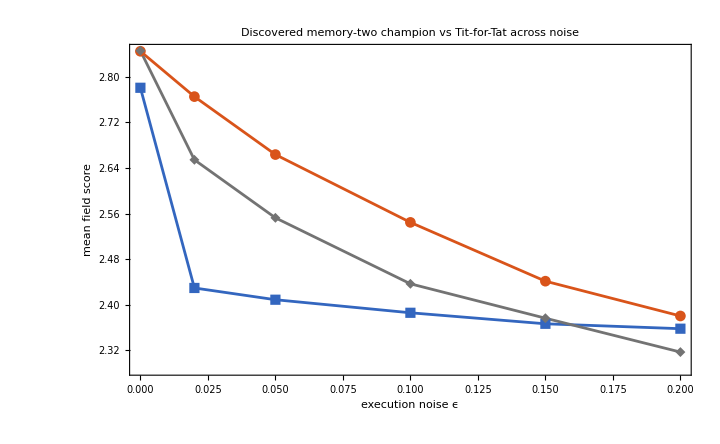

```mathematica
PostFigures`championVsTFT[]
```

The 8-hour memory-two champion (orange) vs Tit-for-Tat and the best non-champion strategy, field score across noise. The champion leads everywhere, though its margin over Tit-for-Tat narrows as noise rises.

### How it ranks against the whole field

Dropped into the full panel of 26 strategies (classics, modern entrants and every strategy discovered in this project), re-scored honestly, the memory-two champion finishes first overall – ahead of the self-tuning Adaptive strategy and well clear of Tit-for-Tat in 15th place. The discovered strategies (orange) take six of the top eight places:

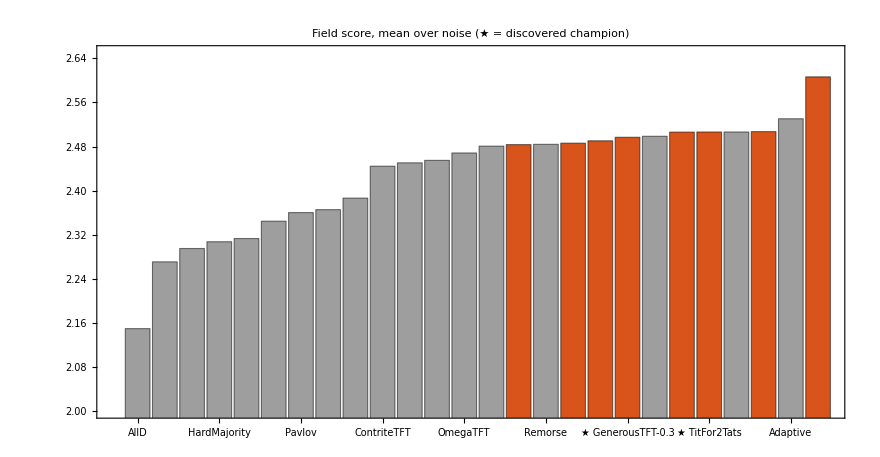

```mathematica
PostFigures`championRanking[]
```

Field score (mean over noise) for all 26 strategies. Orange = discovered by an automated-research loop in this project; ★ marks them. MemTwo-Long, from the 8-hour run, is the single best strategy in the field.

But is it evolutionarily stable? No – and that is the honest, interesting answer. Re-running the ESS invasion analysis with the champion added, MemTwo-Long is not an ESS at any noise level: like every forgiving strategy, a lone unconditional defector can invade a population of it. It is the strongest competitor in the field – it can invade 15–21 of the other 25 strategies – but being the best player is not the same as being uninvadable. The “three meanings of stable” from §9 hold: the best strategy to field and the strategy that cannot be invaded are simply different things.

### Related work: learning versus evolution

A complementary Wolfram Community post by Hyeri Ahn, A Q-Learning Agent Discovers the Optimal Strategy Against Each Opponent in the Prisoner's Dilemma (community.wolfram.com (https://community.wolfram.com/groups/-/m/t/3727339)), reaches the same arena from the opposite direction. There, a single agent uses reinforcement learning (Q-learning) to learn, within its own lifetime, a best response tuned to each specific opponent it faces. Here, a genetic algorithm evolves, across generations, one strategy that does well against an entire field at once.

The contrast is the interesting part. Q-learning exploits a known opponent: told who it is playing, it can find that opponent's weak spot. Our evolutionary search instead seeks robustness: a single rule that must do well against everyone, and – the axis we stress throughout this notebook – across every noise level. The two answer different questions (“how do I beat this player?” versus “what plays well against any player, even through mistakes?”), yet both routes keep rediscovering the same ingredients Axelrod identified by hand: be nice, reciprocate, and forgive. An open question worth posing to the learning approach is how a Q-learner trained in clean play would fare once execution noise is switched on – precisely the regime where, as we have seen, forgiveness stops being optional.

## 11. Three ways to see a strategy

The numbers above settle which strategies win. This section is about seeing why – three visualisations that are rarely brought to the iterated Prisoner's Dilemma, each turning an abstract strategy into a picture you can read at a glance.

### 11.1 Basins of attraction: where does cooperation win?

Take a three-strategy world – AllD, Tit-for-Tat, Generous TFT. Every possible starting mixture is a point in a triangle (the 2-simplex). We colour each starting point by which strategy the replicator dynamics eventually drives it to. The result is a basin map: the geography of who-wins-from-where. Sweeping the noise level shows the cooperative basins (blue, green) give ground to the defector's basin (red) as noise rises – cooperation's “territory” literally shrinks from 99% of the triangle at ϵ=0 to ~64% at ϵ=0.2.

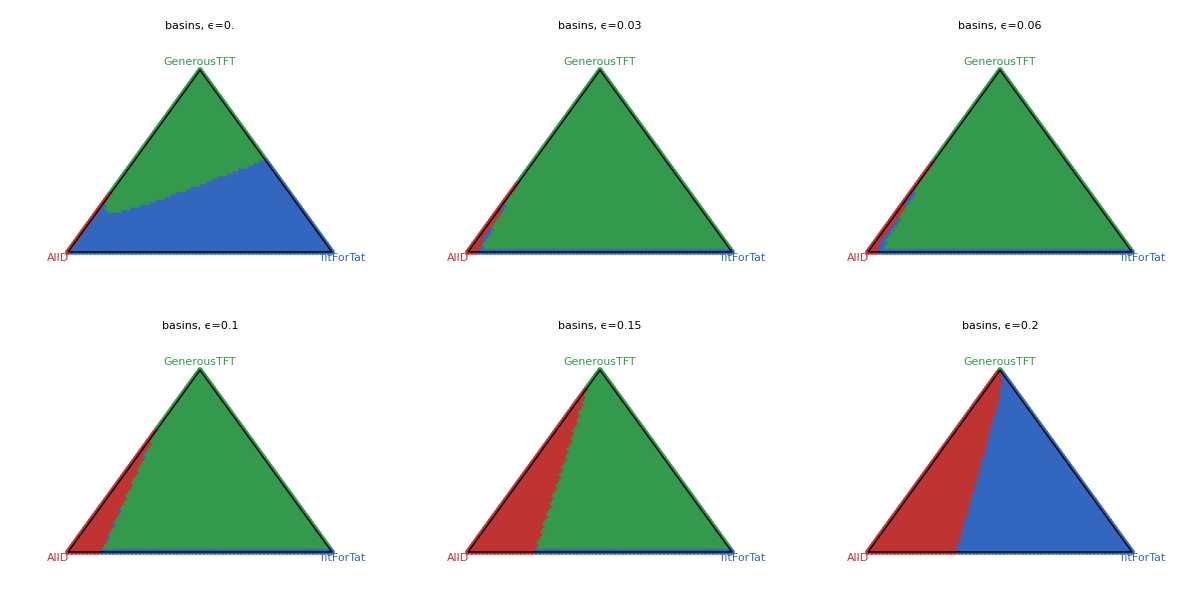

```mathematica
PostFigures`basinsGrid[]
```

Replicator basins of attraction on the three-strategy simplex, across noise. Each point is an initial population mix, coloured by its eventual winner. The defector (AllD, red) basin grows with noise; note how at high noise plain Tit-for-Tat (blue) reclaims territory from Generous TFT as forgiveness stops paying. An animated version is in the repository (basins_vs_noise.gif).

### 11.2 Fingerprints: a strategy's unique signature

A fingerprint (Ashlock, 2008) summarises a strategy as an image. We play the strategy against a one-parameter family of probe opponents – the Joss-Ann transform of Tit-for-Tat, which with probability x just defects and with probability y just cooperates – and record the strategy's score across the whole (x,y) square. Every strategy paints a different picture; the picture exposes its character.

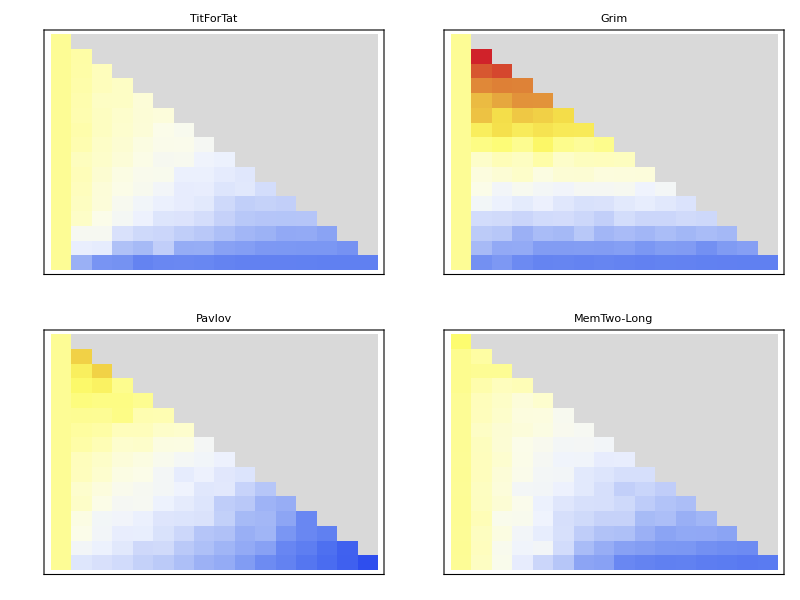

```mathematica
PostFigures`fingerprintsGrid[]
```

Fingerprints at ϵ=0 (warm = high score). Grim's bright hot-spot (top-left) is its signature: it scores enormously against a probe that mostly cooperates but occasionally defects, because it punishes once and the probe keeps cooperating. Tit-for-Tat is smooth and even-handed; Pavlov shows a sharp split between exploiting cooperators and being dragged down by defectors; the memory-two champion is smooth and sink-free – no region where it is badly exploited. (An animation of the champion's fingerprint blurring as noise rises is in the repository: fingerprint_champion_noise.gif.)

### 11.3 A cooperation weather map

Finally, motion. On a 48×48 lattice each cell plays its neighbours and imitates whoever is doing better (§7), now with the discovered memory-two champion added to the mix. Played as a movie – one frame per generation – you watch cooperative clusters nucleate, spread, and defend their borders against invading defectors, side by side at low and high noise. It is the clearest way to feel why spatial structure protects cooperation: cooperators survive by huddling.

```mathematica
PostFigures`spatialMovieFrame[]   (* full movie: spatial_movie_compare.gif *)
```

Spatial IPD as a looping movie: low noise (left) sustains a rich mosaic of cooperative reciprocators; high noise (right) forces them into large defensive clusters of Grim and Tit-for-Tat, but cooperation never collapses. The static call above shows the final frame; the looping animation is spatial_movie_compare.gif (a single-world high-resolution version is spatial_movie.gif).

## 12. Conclusions

Tit-for-Tat is excellent but not optimal. In a cooperative field, more forgiving reciprocators (Generous TFT, Tit-for-2-Tats) edge it out – and extortion finishes last.

Forgiveness must be patient – and, with more memory, discriminating. The autoresearch loop found two-strikes tolerance (Tit-for-2-Tats) beats every reflexive scheme; a self-tuning strategy that estimates the noise also beats TFT; and the 8-hour memory-two search went further still, learning to forgive an isolated (noise-like) defection while punishing a sustained one – the single best strategy in the whole field.

More search keeps paying, but with diminishing, honest returns. Eight hours of evolutionary search over a 17-dimensional space did beat every hand-designed and short-search strategy – yet the gain over a two-minute search was modest, the run converged well before its budget, and fixed-seed fitness had to be discounted by fresh-seed re-evaluation to report an honest number. Automated discovery works; it is not magic.

“Stable” has three answers. ESS admits cooperation at zero noise but collapses to a lone defector under noise; replicator-from-cooperative-start gives generous reciprocity collapsing to Grim under noise; spatial structure gives reciprocator clusters that survive. All noise-dependent, and they disagree.

Population structure changes the effect of noise. Well-mixed: noise drives cooperation to collapse. Spatial: clustering keeps it resilient, degrading gracefully instead of collapsing.

Many roads, one lesson. Fixed-target search, finite-state GP, replicator and Moran dynamics, open-ended co-evolution, and ESS analysis all converge: forgiveness is the answer to noise – until noise is so high that nothing sustains cooperation in a well-mixed world.

## Reproducing this work

Everything here is a few seconds to a few minutes of Wolfram Language – no external data, no API keys. The full source is on GitHub.

wolframscript -file tests/sanity.wls            # correctness checks
wolframscript -file wolfram/tournament.wls      # round-robin ranking
wolframscript -file wolfram/evolution.wls       # replicator + Moran vs noise
wolframscript -file wolfram/discover.wls         # memory-one discovery
wolframscript -file autoresearch/run_search.wls  # autoresearch champions
wolframscript -file wolfram/fsm_discover.wls     # evolve finite-state machines
wolframscript -file wolfram/spatial.wls          # spatial / lattice evolution
wolframscript -file wolfram/coevolution.wls      # Red-Queen co-evolution
wolframscript -file wolfram/ess.wls              # ESS invasion analysis
autoresearch/supervise.sh 28800                  # 8h memory-two search (zombie-safe)
wolframscript -file wolfram/champion_analysis.wls # rank champions vs the field
wolframscript -file wolfram/special_basins.wls    # basins of attraction (+ gif)
wolframscript -file wolfram/special_fingerprints.wls # Ashlock fingerprints (+ gif)
wolframscript -file wolfram/special_spatial_movie.wls # cooperation weather map (gif)
wolframscript -file wolfram/figures.wls          # regenerate base figures

Built entirely in the Wolfram Language. The strategy-discovery and autoresearch loops borrow the propose → evaluate → accept shape of automated-research scaffolds, re-implemented natively in WL.